```mathematica
Solve[p==m b c/Sqrt[1-b^2],b]
```

{{b→-p/(√(c^2 m^2+p^2))},{b→p/(√(c^2 m^2+p^2))}}

```mathematica
1/(p/(√(c^2 m^2+p^2)))/.(p->h/l)
```

(l √(h^2/l^2+c^2 m^2))/h

```mathematica
%//FullSimplify
```

(l √(h^2/l^2+c^2 m^2))/h

```mathematica
Sqrt[1+(c^2*l^2*m^2)/h^2]
```

√(1+(c^2 l^2 m^2)/h^2)

300000000

6.6×10^-34

1.2×10^-39

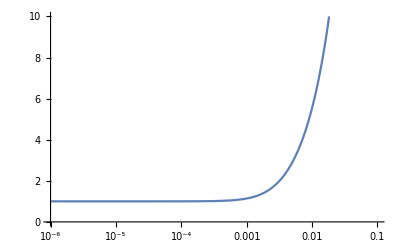

```mathematica
c=3*10^8
h=6.6*10^-34
m=1.2*10^-39
LogLinearPlot[√(1+(c^2 l^2 m^2)/h^2),{l,10^-6,.1},PlotRange->{{10^-6,.1},{0,10}}]
```

```mathematica
Solve[√(1+(c^2 l^2 m^2)/h^2)==n,m]
```

{{m→-(h √(-1+n^2))/(c l)},{m→(h √(-1+n^2))/(c l)}}

```mathematica
InputForm[(h √(-1+n^2))/(c l)]
```

(h*Sqrt[-1 + n^2])/(c*l)

planck constant * sqrt(1.9^2-1)/(speed of light * 100 microns) in eV/c^2

WolframAlphaQueryResults